# Crystal Field Theory – Stevens Operators and Ho/Pt(111)

We show the formulation of effective crystal field Hamiltonians using Stevens operator equivalents [Proc. Phys Soc Sect A 65, 209 (1952)https://iopscience.iop.org/article/10.1088/0370-1298/65/3/308], on the example of single Ho atoms on a clean Pt(111) surface. This system was shown to exhibit localized and well-defined magnetic moments with lifetimes of the order of minutes [Nature 503, 242–246 (2013)https://www.nature.com/articles/nature12759?draft=collection]. Pt crystallizes in an fcc lattice and hence, the (111) surface exhibits a triangular symmetry with the symmetry group C3v.

-Graphics-

GTCrystalFieldpaclet:GroupTheory/ref/GTCrystalFieldGroupTheory Package Symbol | gives the crystal field Hamiltonian for a certain group up to a maximal angular momentum quantum number.
GTStevensOperatorpaclet:GroupTheory/ref/GTStevensOperatorGroupTheory Package Symbol | calculates matrix elements over Stevens operator equivalents

Qualitative analysis. We start with a qualitative analysis of the system. Ho is a rare earth atom with 10 electrons in the f-shell [J.Phys. : Condens.Matter 18 6329 (2006)https://iopscience.iop.org/article/10.1088/0953-8984/18/27/015/meta]. The f-orbitals are spin-orbit split into orbitals with j = 5/2 and j = 7/2, with the j = 5/2 orbital being lower in energy. According to Hunds rule, 6 electrons occupy the j = 5/2 orbital while the remaining 4 electrons occupy the j = 7/2 level with the magnetic quantum numbers m = 7/2, m = 5/2, m = 3/2, m = 1/2. Hence, as a result, a total angular momentum of j = 8 (7/2 + 5/2 + 3/2 + 1/2) arises for the ground state multiplet. We discuss the splitting of this multiplet if the symmetry is lowered to a trigonal symmetry by means of representation theory. C_(3v) is installed using the command GTInstallGrouppaclet:GroupTheory/ref/GTInstallGroupGroupTheory Package Symbol and it' s character table is obtained using GTCharacterTablepaclet:GroupTheory/ref/GTCharacterTableGroupTheory Package Symbol.

```mathematica
Needs["GroupTheory`"]
```

```mathematica
c3v=GTInstallGroup[C3v]
```

The standard representation has changed to O(3)

{Ee,(C^)_(3z)^-1,(C^)_(3z)^,(IC^)_(2D)^,(IC^)_(2C)^,(IC^)_(2y)^}

```mathematica
ct=GTCharacterTable[c3v,GOIrepNotation->"Mulliken"];
```

| Ee | 2 (C^)_(3z)^-1 | 3 (IC^)_(2D)^
A_1 | 1 | 1 | 1
A_2 | 1 | 1 | -1
E | 2 | -1 | 0

C_1 = {Ee}

C_2 = {(C^)_(3z)^-1,(C^)_(3z)^}

C_3 = {(IC^)_(2D)^,(IC^)_(2C)^,(IC^)_(2y)^}

Without the Pt surface, Ho would have an O(3) symmetry where the irreducible representations are denoted by the angular momentum quantum number. The characters of the irreducible representation with j = 8 for the symmetry elements in the three classes of C_(3v) are obtained using GTAngularMomentumCharspaclet:GroupTheory/ref/GTAngularMomentumCharsGroupTheory Package Symbol. This representation is reducible if the symmetry is lowered to C_(3v), where the corresponding decomposition into irreducible representations of C_(3v) is obtained using GTIreppaclet:GroupTheory/ref/GTIrepGroupTheory Package Symbol. The 2*j + 1 - dimensional (17 - dimensional) angular momentum representation decomposes into 3 times A_1, 2 times A_2, and 6 times E. Hence, we expect 5 non-degenerate levels and 6 two-fold degenerate levels.

```mathematica
j8chars=GTAngularMomentumChars[ct[[1]],j=8]
```

{17,5-3 ⅈ (-ⅈ+√3)+3 ⅈ (ⅈ+√3),1}

```mathematica
GTIrep[j8chars,ct]
```

3 A_1⊕2 A_2⊕6 E

{3,2,6}

Quantitative analysis. To obtain the spectrum of Ho/Pt(111) quantitatively we formulate an effective crystal field Hamiltonian using GTCrystalFieldpaclet:GroupTheory/ref/GTCrystalFieldGroupTheory Package Symbol. To apply Stevens operators in the second step, we need a real basis, which is obtained by specifying the option GOHarmonicspaclet:GroupTheory/ref/GOHarmonicsGroupTheory Package Symbol. We furthermore use a cut-off angular momentum of l = 6. Also, for convenience, we apply a slight redefinition of the standard parameters A[l_,m_] -> B[l,m] r^l.

```mathematica
vcrtmp=Simplify[GTCrystalField[c3v,6,GOHarmonics->"Real"]/.A[l_,m_]->B[l,m]/r^l]
```

B[0,0] S[0,0]+B[2,0] S[2,0]+B[4,-3] S[4,-3]+B[4,0] S[4,0]+B[6,-6] S[6,-6]+B[6,-3] S[6,-3]+B[6,0] S[6,0]

The crystal field Hamiltonian is now formulated in terms of crystal field parameters B[l, m] and crystal field operators S[l, m]. We replace the operators S[l, m] by Stevens operators using the command GTStevensOperatorpaclet:GroupTheory/ref/GTStevensOperatorGroupTheory Package Symbol. For the B[l, m] we use the respective values from Ref. [Nature 503, 242–246 (2013)https://www.nature.com/articles/nature12759?draft=collection].

```mathematica
vcr=vcrtmp/.S[l_,m_]:>GTStevensOperator[l,m,j];
```

```mathematica
Amat=SetAccuracy[vcr/.{B[0,0]->0,B[2,0]->-239.068*10^-6,
B[4,0]->85.9023*10^-9,B[4,-3]->293.446*10^-9,B[6,0]->0.186782*10^-9,
B[6,-3]->-1.96786*10^-9,B[6,-6]->0.630483*10^-9},40];
```

The Hamiltonian is diagonalized with the Mathematica command Eigensystem. The eigenvectors are used to calculate the expectation value of the magnetic moment in z - direction  <J_z> . The plot reveals a 2-fold degenerate ground state with <J_z>=±8. In agreement with the qualitative analysis, we find 6 two-fold degenerate levels with nonzero <J_z>, as well as five non - degenerate levels with <J_z> = 0.

```mathematica
{ev,evec}=Eigensystem[Amat]//Chop;
```

```mathematica
Jz[j_]:=DiagonalMatrix[Table[m,{m,-j,j}]];
eval=Table[{Conjugate[evec[[i]]].Jz[j].evec[[i]],
(ev[[i]]-Min[ev])*1000},{i,1,Length[evec]}]//Chop;
```

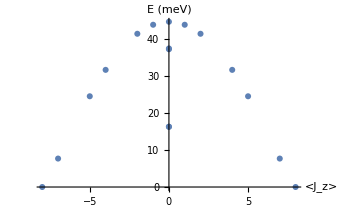

```mathematica
ListPlot[eval//Chop,AxesLabel->{"<J_z>","E (meV)"}]
```

```mathematica
TableForm[Sort[eval,#1[[2]]<#2[[2]]&]//Chop,TableHeadings->{None,{"<Jz> (ℏ)","E (meV)"}}]
```

<Jz> (ℏ) | E (meV)
-7.9999445378167476694770549437819612 | 0
7.9999445378167476694770549437819612 | 0
6.9999888253503987726625738588003967 | 7.706564603496895826564661726933078
-6.9999888253503987726625738588003768 | 7.706564603496895826564661726933078
0 | 16.32554584502505083898672060509132
0 | 16.32585016592244810230218488104243
-4.9987519839945242401232418741665648 | 24.580641338275704916773570476050445
4.9987519839945242401232418741665648 | 24.580641338275704916773570476050445
3.9967066518596124574853446483680036 | 31.734511546803802035954937979505492
-3.9967066518596124574853446483680036 | 31.734511546803802035954937979505492
0 | 37.320099087728624258683275828345655
0 | 37.530640146138221217848296667791486
-1.9952316587735570398918968998048241 | 41.50924884748271249023194497007723
1.9952316587735570398918968998048241 | 41.50924884748271249023194497007723
-0.99723270337481771934427521058494985 | 43.952992774284366441537195943658243
0.99723270337481771934427521058494986 | 43.952992774284366441537195943658243
0 | 44.76555918117189192966570303872584

| Related Guides
▪W. Hergert, R. M. Geilhufe, Group Theory in Solid State Physics and Photonics: Problem Solving with Mathematica, Wiley-VCH, ISBN: 978-3-527-41133-7 (2018).http://gtpack.org/book/